{c→21.1115,k→0.397348,b→15.8488}

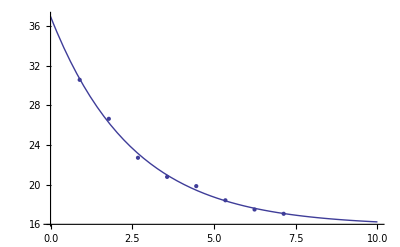

```mathematica
data = {
{0.8914285714,30.5705142857},
{1.7828571428,26.6410285714},
{2.6742857142,22.7115428571},
{3.5657142856,20.7820571428},
{4.457142857,19.8525714285},
{5.3485714284,18.4230857142},
{6.2399999998,17.4935999999},
{7.1314285712,17.0641142856}
};
model = c*Exp[-k*x]+b;
fit = FindFit[data,model,{c,k,b},x,MaxIterations->100000]
ffit = model/. fit;
plot = Plot[ffit, {x,0,10}];
pdata = ListPlot[data];
Show[plot,pdata]
```